```mathematica
(*Definicja równania parametrycznego*)conchoida[a_]:={1/Cos[t]+a*Cos[t],Sin[t]+a*Sin[t]};

(*Wyznaczanie minimalnej rozmaitości algebraicznej*)
GroebnerBasis[Thread[conchoida[a]-{r,θ}],{r,θ},{Cos[t],Sin[t]}]
```

```mathematica
narysowc conchoidy (chyba zle) i wylicz baze grobnera
```

```mathematica
(*Define the variables*){x,y,X,Y,a}={x,y,X,Y,a};
x=(1+a)(Cos[t])^2+Sin[t]Cos[t];
y=(1+a)Cos[t]Sin[t]+ (Sin[t])^2;
X =Cos[t];
Y =Sin[t];
(*Define the equations*)
eq1=(1+a)*(1-Y^2)+X*Y-x==0;
eq2=(1+a)*X*Y+(1-X^2)-y==0;

(*Define the ordering*)
order={x,y,X,Y};

(*Compute the Groebner basis*)
groebner=GroebnerBasis[{eq1,eq2},{x,y,X,Y},a,MonomialOrder->Lexicographic];

(*Display the Groebner basis*)
groebner
```

General::ivar: (1+a) Cos[t] Sin[t]+Sin[t]^2 is not a valid variable.

GroebnerBasis[{-(1+a) Cos[t]^2+(1+a) (1-Sin[t]^2),1-Cos[t]^2-Sin[t]^2},{(1+a) Cos[t]^2+Cos[t] Sin[t],(1+a) Cos[t] Sin[t]+Sin[t]^2,Cos[t],Sin[t]},a,MonomialOrder→Lexicographic]

```mathematica
a Cos[t]+Sec[t]
```

a Cos[t]+Sec[t]

```mathematica
(*Definiujemy funkcję dla r*)f[a_,t_]:=1/Cos[t]+a*Cos[t]

(*Narysowanie wykresów dla różnych wartości a*)
Plot3D[f[a,t],{a,-4,3},{t,0,2 Pi},AxesLabel->{"a","t","r"}]
```

-Graphics3D-

```mathematica
(*Definiujemy równanie parametryczne*)eqn=r==1/Cos[t]+a*Cos[t];

(*Obliczamy bazę Grobnera*)
GroebnerBasis[{eqn},{r,t,a}]

(*Narysowanie krzywych konchoidealnych w przestrzeni trójwymiarowej*)
Show[Table[ParametricPlot3D[{Cos[t],t,1/Cos[t]+a*Cos[t]},{t,0,2 Pi},PlotStyle->Hue[Abs[a]/4],PlotLabel->StringJoin["a = ",ToString[a]]],{a,{-4,-2,0,1,2,3}}],Boxed->False,AxesLabel->{"x","t","r"}]
```

{r-a Cos[t]-Sec[t]}

-Graphics3D-

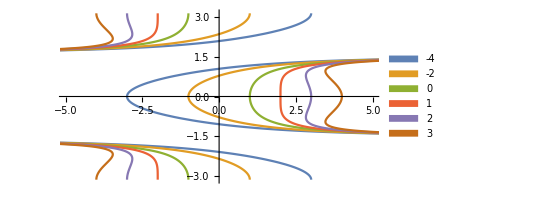

```mathematica
Clear["Global`*"]
conchoid[a_]:=ParametricPlot[{1/Cos[t]+a Cos[t],t},{t,-Pi,Pi},AspectRatio->1/2,PlotStyle->Switch[a,
-4,ColorData[97][1],
-2,ColorData[97][2],
_,ColorData[97][a+3]]]

legendLabels=SwatchLegend[{
ColorData[97][1],
ColorData[97][2],
ColorData[97][3],
ColorData[97][4],
ColorData[97][5],
ColorData[97][6]},
{-4,-2,0,1,2,3},
LegendMarkerSize->{20,20}];

plots=Table[conchoid[a],{a,{-4,-2,0,1,2,3}}];
Legended[Show[plots, PlotRange->{{-5,5},Automatic}],Placed[legendLabels,Right]]
```

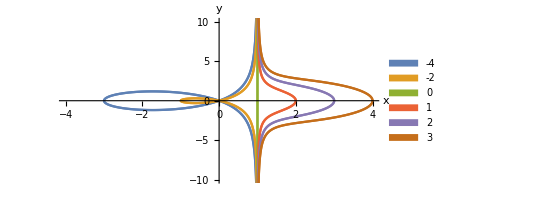

```mathematica
Clear["Global`*"]

conchoid[a_]:=ParametricPlot[{1+a Cos[t]^2,Tan[t]+a Cos[t] Sin[t]},{t,-Pi,Pi},
AspectRatio->1/2,PlotStyle->Switch[a,
-4,ColorData[97][1],
-2,ColorData[97][2],
_,ColorData[97][a+3]],
AxesLabel->{"x","y"}
]

legendLabels=SwatchLegend[{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5],ColorData[97][6]},{-4,-2,0,1,2,3},LegendMarkerSize->{20,20}]

plots=Table[conchoid[a],{a,{-4,-2,0,1,2,3}}];

Legended[Show[plots,PlotRange->{{-4,4},{-10,10}}],Placed[legendLabels,Right]]
```

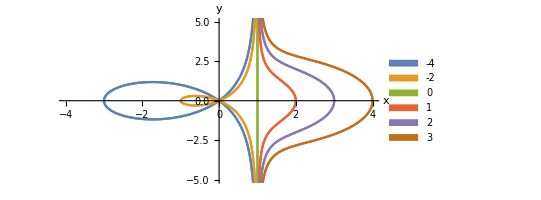

```mathematica
Clear["Global`*"]

conchoid[a_]:=ParametricPlot[{1+a Cos[t]^2,Tan[t]+a Cos[t] Sin[t]},{t,-Pi,Pi},
AspectRatio->1/2,PlotStyle->Switch[a,
-4,ColorData[97][1],
-2,ColorData[97][2],
_,ColorData[97][a+3]],
AxesLabel->{"x","y"}
]

legendLabels=SwatchLegend[{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5],ColorData[97][6]},{-4,-2,0,1,2,3},LegendMarkerSize->{20,20}]

plots=Table[conchoid[a],{a,{-4,-2,0,1,2,3}}];

Legended[Show[plots,PlotRange->{{-4,4},{-5,5}}],Placed[legendLabels,Right]]
```